```mathematica
plotVals={};

For[q=1,q≤15,q++,For[p=1,p≤q,p++,
If[CoprimeQ[p,q]==False,Continue,
α=p/q;
M[m_]:={{ϵ-2*Cos[2π*α*m-1/(2*q)],-1},{1,0}};
Qtr=Tr[Apply[Dot,Map[M,Range[1,q,1]]]];
rts=(NRoots[Qtr==4,ϵ]||NRoots[Qtr==-4,ϵ])[[All,2]]/.Or->List;
rts=Sort[Select[rts,Im[#]==0 &],#2>#1 &];
L=Length[rts]; 
evenRts = Take[rts,{2,L,2}];
oddRts = Take[rts,{1,L-1,2}];
limits = Transpose[{oddRts,evenRts}];
createLims[limits_]:=Range[limits[[1]],limits[[2]],0.01];
energies=Flatten[Map[createLims,limits]];
plotVals=Flatten[{plotVals,Transpose[{energies,ConstantArray[α,Length[energies]]}]},1]//N;
]]]
```

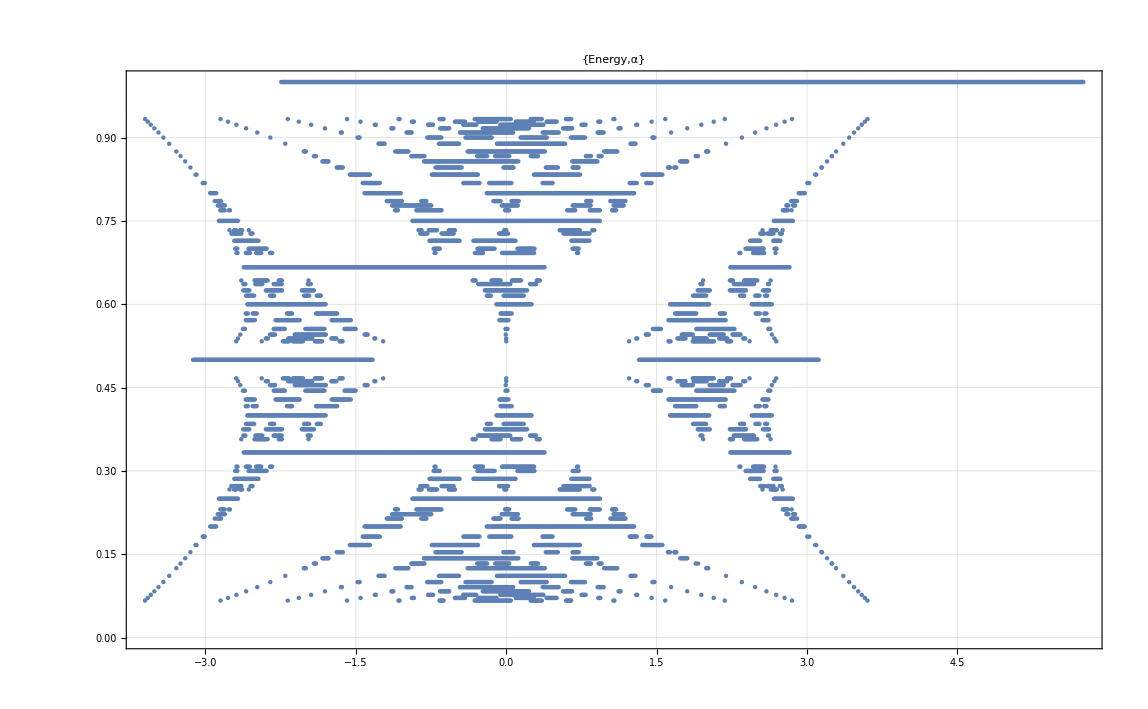

```mathematica
ListPlot[plotVals,Frame->True,GridLines->Automatic,ImageSize->Large,PlotLabel->{"Energy","α"}]
```